```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
StringTake[FileNames["*.txt"],{1,3}]
```

{D13,D15,D33,D35,F15,F17,F35,F37,G17,G19,G37,G39,H19,H39,P11,P13,P31,P33,S11,S31}

```mathematica
names={"S11","S31","P11","P31","P13","P33","D13","D33","D15","D35","F15","F35","F17","F37","G17","G37","G19","G39","H19","H39"};
```

```mathematica
data=Import[#<>".txt","Data"]&/@names;
```

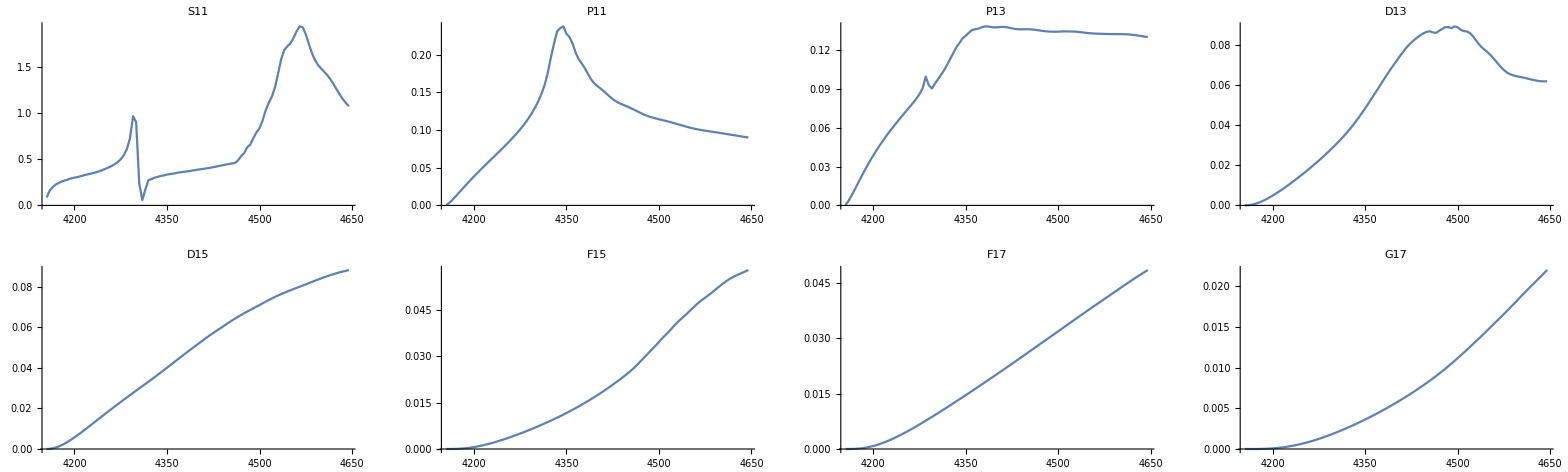

```mathematica
GraphicsGrid[Partition[Flatten[ParallelTable[ListLinePlot[data[[i,;;,{1,4}]],PlotRange->All,PlotLabel->names[[i]]],{i,1,20,2}],1],4]]
```

```mathematica
GraphicsGrid[Partition[Flatten[ParallelTable[ListLinePlot[Table[Callout[data[[i,j,{2,3}]],data[[i,j,1]]],{j,99}],PlotRange->All,PlotLabel->names[[i]]],{i,1,20,2}],1],4]]
```

-Graphics-